```mathematica
Import["C:\Users\cestdiego\Documents\prueba.xlsx", {"Data",1,{1,10},4}]
```

{,29.}

```mathematica
s =Import["/home/io/Documents/Projects/Dropbox/Laboratorios/Laboratorio-Fisica-Intermedia-UNI/Fïsica Intermedia Exp4. Conductividad del Genrmanio.xlsx"];
```

```mathematica
logT = s[[2]][[Range[8,129],10]];
```

```mathematica
logConduct = s[[2]][[Range[8,129],11]];
```

```mathematica
logConduct[[1]]
```

4.44646

```mathematica
SWOLO = Table[{logT[[n]],logConduct[[n]]},{n,90,122}];
```

```mathematica
SWOLO;
```

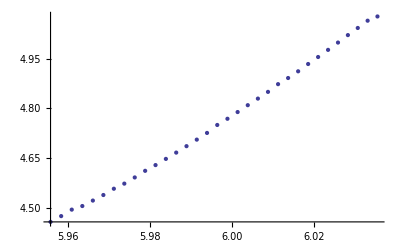

```mathematica
ListPlot[SWOLO]
```

```mathematica
Fit[SWOLO,{1,x},x]
```

-42.7214+7.9179 x

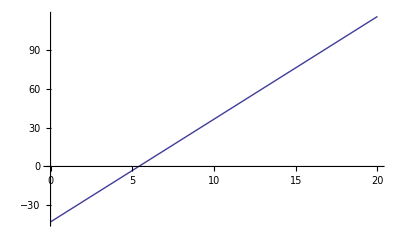

```mathematica
Plot[%,{x,0,20}]
```

```mathematica
SWAG = Table[{logT[[n]],logConduct[[n]]},{n,1,40}];
```

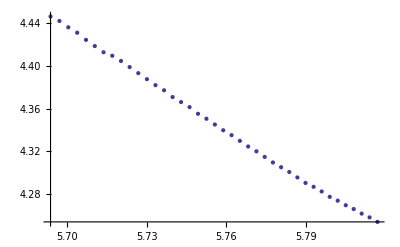

```mathematica
ListPlot[SWAG]
```

```mathematica
Fit[SWAG,{1,x},x]
```

13.5011-1.59049 x